# Problem trzech ciał

## Projekt zaliczeniowy z NOF - Paweł Konopka

## Setup

### Constants

```mathematica
G=6.6743*^-11;
MassOfTheSun = 1.989*^30;
```

### Data structures

```mathematica
Body [params_] := Append[
params, {
"position" -> N @ params["position"],
"velocity" -> N @ params["velocity"],
"positionHistory" -> {}
}]
```

### Simulation code

```mathematica
CalculateAcceleration[body_, other_] := Module[{distVec},
distVec = body["position"] - other["position"];

- G * other["mass"] / Norm[distVec]^3 * distVec
]

SimulateStep[body_, remainingBodies_, dt_] := Module[
{accelerationVec, newVelocityVec, newPositionVec},
accelerationVec = Total[Map[
otherBody |-> CalculateAcceleration[body, otherBody],
remainingBodies
]];
newVelocityVec = body["velocity"] + accelerationVec * dt;
newPositionVec = body["position"] + newVelocityVec * dt;

Append[body, {
"velocity" -> newVelocityVec,
"position" -> newPositionVec,
"positionHistory" -> Append[body["positionHistory"], body["position"]]
}]
]

Simulate[initialBodies_, totalTime_, nSteps_] := Module[{dt, time, bodies},
dt = N[totalTime / nSteps];
time = 0;
bodies = initialBodies;

While[time < totalTime,
bodies = MapIndexed[
{body, idxArr} |-> Module[{index},
{index} = idxArr;
SimulateStep[body, Delete[bodies, index], dt]
],
bodies
];
time += dt;
];

bodies
]
```

### Visualization code

```mathematica
PlotBodies[bodies_] := Graphics[
Map[
body |-> {
PointSize[body["mass"]^(1/3) / 4*^11],
body["color"],
Point[body["position"]],
Line[body["positionHistory"]]
},
bodies
],
Axes->True,
AxesLabel-> {"x [m]", "y [m]"},
GridLines->Automatic
]

PlotFrame[bodies_, frame_] := PlotBodies @ Map[
body |-> Append[body, {
"position" -> body["positionHistory"][[frame]],
"positionHistory" -> body["positionHistory"][[;;frame]]
}],
bodies
]

AnimateBodies[bodies_] := Module[{numberOfFrames},
numberOfFrames = Length[First[bodies]["positionHistory"]];
 Animate[
PlotFrame[bodies, i],
{i, 1, numberOfFrames, 1},
AnimationRunning->False,
AnimationRate->numberOfFrames / 100
]
]
```

## Simulations

### Simulation I

```mathematica
bodies1 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {0, 1*^4},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {1*^10, 1*^10},
"velocity" -> {-1*^5, 0},
"color" -> Blue,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {1*^10, 0},
"velocity" -> {5*^4, -5*^4},
"color" -> DarkGreen,
"mass" -> MassOfTheSun
|>]
};

simulatedBodies1 = Simulate[bodies1,1000000, 5000];
AnimateBodies [simulatedBodies1]
```

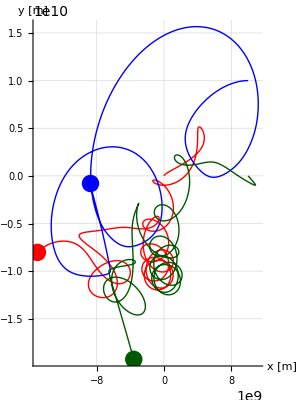

```mathematica
PlotFrame[simulatedBodies1, 4750]
```

### Simulation II

```mathematica
bodies2 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {5*^4, 1*^4},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {1*^10, 0},
"velocity" -> {-4*^4, 0},
"color" -> Blue,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {0.5*^10, 0.7*^10},
"velocity" -> {-8*^4, -2.5*^4},
"color" -> DarkGreen,
"mass" -> MassOfTheSun
|>]
};

simulatedBodies2 = Simulate[bodies2,1500000, 6000];
AnimateBodies[simulatedBodies2]
```

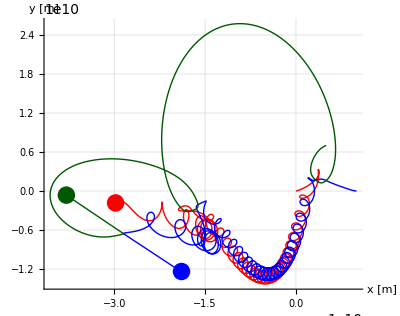

```mathematica
PlotFrame[simulatedBodies2, 5815]
```

### Simulation III

```mathematica
bodies3 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {0, 0},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {0, 2*^9},
"velocity" -> {3*^5,0},
"color" -> Blue,
"mass" -> MassOfTheSun / 10^4
|>],
Body[<|
"position" -> {0, -5*^9},
"velocity" -> {-2*^5,0},
"color" -> DarkGreen,
"mass" -> MassOfTheSun / 10^4
|>]
};

simulatedBodies3 = Simulate[bodies3,10000000, 5000];
AnimateBodies[simulatedBodies3]
```

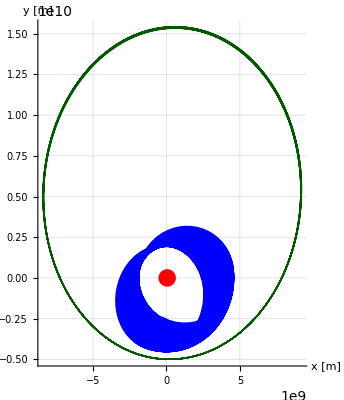

```mathematica
PlotFrame[simulatedBodies3, 2500]
```

### Example IV

```mathematica
bodies4 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {5*^4, 0},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {0, 1*^10},
"velocity" -> {-5*^4, 0},
"color" -> Blue,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {5*^8, 1*^10},
"velocity" -> {-5*^4, -5*^5},
"color" -> DarkGreen,
"mass" -> MassOfTheSun / 10^4
|>]
};

simulatedBodies4 = Simulate[bodies4,1500000, 6000];
AnimateBodies[simulatedBodies4]
```

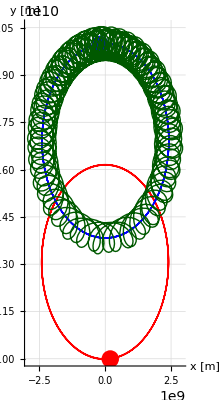

```mathematica
PlotFrame[simulatedBodies4, 3000]
```

### Example V

```mathematica
bodies5 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {5*^4, 0},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {0, 1*^10},
"velocity" -> {-5*^4, 0},
"color" -> Blue,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {2*^9, 1*^10},
"velocity" -> {-8*^3, -2.5*^5},
"color" -> DarkGreen,
"mass" -> MassOfTheSun / 10^4
|>]
};

simulatedBodies5 = Simulate[bodies5,300000, 6000];
AnimateBodies[simulatedBodies5]
```

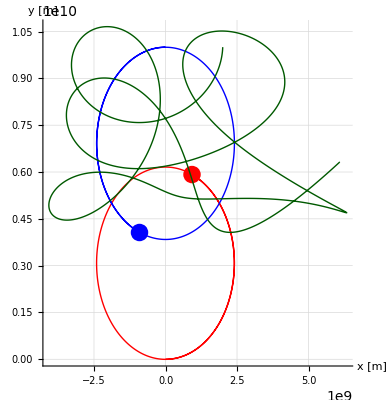

```mathematica
PlotFrame[simulatedBodies5, 5500]
```

### Example VI

```mathematica
bodies6 = {
Body[<|
"position" -> {0, 0},
"velocity" -> {6*^3, 0},
"color" -> Red,
"mass" -> MassOfTheSun
|>],
Body[<|
"position" -> {0, 1*^10},
"velocity" -> {-6*^4, 0},
"color" -> Blue,
"mass" -> MassOfTheSun / 10
|>],
Body[<|
"position" -> {4*^8, 1*^10},
"velocity" -> {-6*^4, 1.5*^5},
"color" -> DarkGreen,
"mass" -> MassOfTheSun / 10^4
|>]
};

simulatedBodies6 = Simulate[bodies6,1000000, 4000];
AnimateBodies[simulatedBodies6]
```

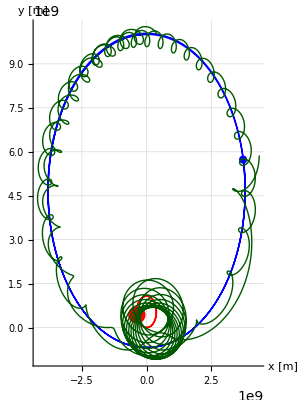

```mathematica
PlotFrame[simulatedBodies6, 2510]
```

## Animation export

```mathematica
GifFPS = 25;
GifTotalDurationSeconds = 30;

GetFrameTable[bodies_, totalRawFrames_] := Module[{targetFrameCount,stepSize},
targetFrameCount=GifFPS*GifTotalDurationSeconds;
stepSize = N[(totalRawFrames-1)/(targetFrameCount-1)];

ParallelTable[
PlotFrame[bodies,Round[i]],
{i,1.0,totalRawFrames,stepSize},
Method->"FinestGrained"
]
]

ExportAsGif[bodies_, filename_] := Module[{numberOfFrames, frames},
numberOfFrames = Length[First[bodies]["positionHistory"]];
frames = GetFrameTable[bodies, numberOfFrames];

Export[
filename <> ".gif",
frames,
"DisplayDurations" -> 1.0/GifFPS,
"AnimationRepetitions" -> 1
]
]
```

```mathematica
(*
ExportAsGif[simulatedBodies1, "simulation1"]
ExportAsGif[simulatedBodies2, "simulation2"]
ExportAsGif[simulatedBodies3, "simulation3"]
ExportAsGif[simulatedBodies4, "simulation4"]
ExportAsGif[simulatedBodies5, "simulation5"]
ExportAsGif[simulatedBodies6, "simulation6"]
*)
```